```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["VariationalMethods`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
ClearAll[Sd,γm,γp,q2SolDEL,h,k,m,r,q0,v0,q1,q2,qrecursive,σRK]
```

```mathematica
(*k=0;*)
```

```mathematica
(* r=0;*)
```

### Definition of the continuous Lagrangian and Rayleigh potential

```mathematica
L[q_,v_]:=1/2*m*v^2-1/2*k*q^2
```

```mathematica
R[q_,v_]:=1/2*r*v^2
```

```mathematica
f[q_,v_]=-D[R[q,v],v]
```

-r v

### Midpoint discrete Lagrangians and Rayleigh potential

```mathematica
(*Ld[q0_,q1_]:=1/2*m*((q1-q0)/h)^2-1/2*k*((q1+q0)/2)^2*)
```

```mathematica
(*Rd[q0_,q1_]:=1/2*r*((q1-q0)/h)^2*)
```

```mathematica
Ld[q0_,q1_]=h*L[(q0+q1)/2,(q1-q0)/h]
```

h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)

```mathematica
Rd[q0_,q1_]=h^2/2*R[(q0+q1)/2,(q1-q0)/h]
```

1/4 (-q0+q1)^2 r

```mathematica
Ldp[q0_,q1_]=Ld[q0,q1]+Rd[q0,q1]
```

h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)+1/4 (-q0+q1)^2 r

```mathematica
Ldm[q0_,q1_]=Ld[q0,q1]-Rd[q0,q1]
```

h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)-1/4 (-q0+q1)^2 r

```mathematica
fdp[q0_,q1_]=h/2*f[(q0+q1)/2,(q1-q0)/h]
```

-1/2 (-q0+q1) r

```mathematica
fdm[q0_,q1_]=h/2*f[(q0+q1)/2,(q1-q0)/h];
```

```mathematica
fdp[q0,q1]==-D[Rd[q0,q1],q1]&&fdm[q0,q1]==D[Rd[q0,q1],q0]//Simplify
```

True

### Discrete Euler-Lagrange equations

```mathematica
DEL:=D[Ldm[Q0,Q1],Q1]+D[Ldp[Q1,Q2],Q1]==0
```

```mathematica
q2SolDEL[q0_,q1_]:=Solve[DEL,Q2][[1]][[1]][[2]]/.Q0->q0/.Q1->q1
```

```mathematica
q2SolDEL[q1,q2]
```

(-h^2 k q1-4 m q1-2 h^2 k q2+8 m q2+2 h q1 r)/(h^2 k+4 m+2 h r)

### Legendre transforms and Hamiltonian flow

```mathematica
Legp[q0_,q1_]={q1,D[Ldm[q0,q1],q1]}
```

{q1,h ((m (-q0+q1))/h^2-1/4 k (q0+q1))-1/2 (-q0+q1) r}

```mathematica
Legm[q0_,q1_]={q0,-D[Ldp[q0,q1],q0]}
```

{q0,-h (-(m (-q0+q1))/h^2-1/4 k (q0+q1))+1/2 (-q0+q1) r}

```mathematica
inverseLegm1[q0_,p0_]=Solve[Legm[q0,q1][[2]]==p0,q1][[1,1,2]]
```

(4 h p0-h^2 k q0+4 m q0+2 h q0 r)/(h^2 k+4 m+2 h r)

```mathematica
inverseLegm[q0_,p0_]={q0,inverseLegm1[q0,p0]}
```

{q0,(4 h p0-h^2 k q0+4 m q0+2 h q0 r)/(h^2 k+4 m+2 h r)}

```mathematica
FlowH[q0_,p0_]=Legp[inverseLegm[q0,p0][[1]],inverseLegm[q0,p0][[2]]];
```

```mathematica
Simplify[FlowH[q0,p0]]
```

{(4 h p0-h^2 k q0+4 m q0+2 h q0 r)/(h^2 k+4 m+2 h r),-(h^2 k p0-4 m p0+4 h k m q0+2 h p0 r)/(h^2 k+4 m+2 h r)}

### Discrete action

```mathematica
Sd[q_]:=Sum[Ld[q[[i]],q[[i+1]]],{i,Length[q]-1}]
```

```mathematica
Sd[{q0,q1,q2,q3}]
```

h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)+h ((m (-q1+q2)^2)/(2 h^2)-1/8 k (q1+q2)^2)+h ((m (-q2+q3)^2)/(2 h^2)-1/8 k (q2+q3)^2)

```mathematica
Sdtilde[qA_,qB_]:=Sd[qA]+Sd[qB];
```

```mathematica
Gd[qA_,qB_]:=Sdtilde[qA,qB]-Rd[qA[[-1]],qB[[-1]]];
```

```mathematica
Gd[{q0,q1,q2,q3},{q0,q1,q2,q3,q4}]
```

2 h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)+2 h ((m (-q1+q2)^2)/(2 h^2)-1/8 k (q1+q2)^2)+2 h ((m (-q2+q3)^2)/(2 h^2)-1/8 k (q2+q3)^2)+h ((m (-q3+q4)^2)/(2 h^2)-1/8 k (q3+q4)^2)-1/4 (-q3+q4)^2 r

### Flows and mappings

```mathematica
Γm[qA_,qB_]:=D[Gd[qA,qB],qA[[-1]]];
```

```mathematica
Γp[qA_,qB_]:=D[Gd[qA,qB],qB[[-1]]];
```

```mathematica
γp[q1_,q2_]=Γp[{q0,q1},{q0,q1,q2}];
```

```mathematica
γp[q4,q5]==Γp[{q0,q1,q2,q3,q4},{q0,q1,q2,q3,q4,q5}]
```

True

```mathematica
γm[q0_,q1_,q2_]=Γm[{q0,q1},{q0,q1,q2}]
```

2 h ((m (-q0+q1))/h^2-1/4 k (q0+q1))+h (-(m (-q1+q2))/h^2-1/4 k (q1+q2))+1/2 (-q1+q2) r

```mathematica
γm[q3,q4,q5]==Γm[{q0,q1,q2,q3,q4},{q0,q1,q2,q3,q4,q5}]
```

True

```mathematica
Flowm[q1_,q2_]=FlowH[q2,γp[q1,q2]][[1]];
```

```mathematica
Flowm   [q1,q2]//Simplify
```

(-4 m (q1-2 q2)-h^2 k (q1+2 q2)+2 h q1 r)/(h^2 k+4 m+2 h r)

```mathematica
q2SolDEL[q0,q1]==Flowm[q0,q1]//Simplify
```

True

```mathematica
γm[q0,q1,q2]
```

2 h ((m (-q0+q1))/h^2-1/4 k (q0+q1))+h (-(m (-q1+q2))/h^2-1/4 k (q1+q2))+1/2 (-q1+q2) r

```mathematica
γp[q1,q2]
```

h ((m (-q1+q2))/h^2-1/4 k (q1+q2))-1/2 (-q1+q2) r

### Right discrete Hamiltonian and Hamilton equations

```mathematica
Hdp[q0_,q1_,p1_]:=p1*q1-Ld[q0,q1]
```

```mathematica
Hdp[q0,q1,p1]
```

p1 q1-h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)

```mathematica
Solve[q2==D[Hdp[q1,q2,p2],p2]-D[Rd[q1,q2],q2]/D[γp[q1,q2],q2]/.p2->γp[q1,q2],q2]
```

{{q2→q1}}

### Left discrete Hamiltonian and Hamilton equations

```mathematica
Hdm[q0_,q1_,p0_]=-p0*q0-Ld[q0,q1]
```

-p0 q0-h ((m (-q0+q1)^2)/(2 h^2)-1/8 k (q0+q1)^2)

```mathematica
Hdmimp[q0_,q1_,q2_]=Hdm[q1,q2,γm[q0,q1,q2]]
```

-h ((m (-q1+q2)^2)/(2 h^2)-1/8 k (q1+q2)^2)-q1 (2 h ((m (-q0+q1))/h^2-1/4 k (q0+q1))+h (-(m (-q1+q2))/h^2-1/4 k (q1+q2))+1/2 (-q1+q2) r)

```mathematica
HamiltonEq[q0_,q1_,q2_]:=((q1+D[Hdm[q1,q2,p1],p1])*D[γm[q0,q1,q2],q1]+D[Rd[q1,q2],q1])/.p1->γm[q0,q1,q2]
```

```mathematica
HamiltonEq[q0,q1,q2]
```

-1/2 (-q1+q2) r

```mathematica
Solve[HamiltonEq[q0,q1,q2]==0,q2]
```

{{q2→q1}}

### Continuous Euler-Lagrange equations

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]==0
```

```mathematica
SolsELeq=First@DSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],t];
```

```mathematica
σ[t_]=SolsELeq[[1]][[2]]//Simplify
```

1/(2 √(-4 k m+r^2))ⅇ^(-((r+√(-4 k m+r^2)) t)/(2 m)) ((-1+ⅇ^((√(-4 k m+r^2) t)/m)) q0 r+(1+ⅇ^((√(-4 k m+r^2) t)/m)) q0 √(-4 k m+r^2)+2 (-1+ⅇ^((√(-4 k m+r^2) t)/m)) m v0)

```mathematica
(*σ[0]==q0&&σ[h]==q1//Simplify*)
```

```mathematica
σ[0]==q0&&σ'[0]==v0//Simplify
```

True

Function of r so that we can play with the parameter

```mathematica
Σ[t_,r_]=SolsELeq[[1]][[2]];
```

Energy

```mathematica
EL[q_,v_]=v*D[L[q,v],v]-L[q,v];
```

```mathematica
Energy[t_]=EL[σ[t],σ'[t]]//Simplify;
```

Give values to the constants before plotting

```mathematica
{h=.25,k=1,m=1,r=.5,q0=0,v0=1};
```

```mathematica
q1=Re[σ[h]]
```

0.232566

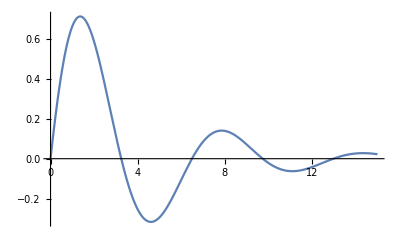

```mathematica
Plot[σ[t],{t,0,15}]
```

```mathematica
Manipulate[Plot[Σ[t,r],{t,0,15}],{r,0,5}]
```

### Runge-Kutta method

```mathematica
(*SolsRungeKutta=NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},
StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitRungeKutta"}}];*)
```

```mathematica
(*σRK[t_]=SolsRungeKutta[[1]][[1]][[2]]*)
```

```mathematica
tend=100;
```

```mathematica
RKsols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q[0]==q0,Q'[0]==v0},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitRungeKutta"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
RKpts=Table[{h*n,RKsols[[n]]},{n,0,Floor[tend/h]}];
```

```mathematica
Eulersols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q[0]==q0,Q'[0]==v0},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitEuler"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
Eulerpts=Table[{h*n,RKsols[[n]]},{n,0,Floor[tend/h]}];
```

```mathematica
(*SolsEuler=First@NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitEuler"
}}];*)
```

```mathematica
(*σEuler[t_]=SolsEuler[[1]][[2]]//Simplify;*)
```

### Continuous vs discrete

```mathematica
qrecursive[0]=q0;
qrecursive[1]=q1;
qrecursive[n_]:=qrecursive[n]=q2SolDEL[qrecursive[n-2],qrecursive[n-1]]
```

```mathematica
discretepts=Table[{h*n,qrecursive[n]},{n,0,Floor[tend/h]}];
```

```mathematica
discretepts[[2]]=={h,Re[σ[h]]}
```

True

```mathematica
discretepts[[3]]
```

{0.5,0.424687}

```mathematica
discretevels=Table[{(discretepts[[n+1,2]]+discretepts[[n,2]])/2,(discretepts[[n+1,2]]-discretepts[[n,2]])/h},{n,1,100}];
```

```mathematica
RKvels=Table[{RKpts[[n,2]],(2(RKpts[[n+1]][[2]]-RKpts[[n-1]][[2]]))/(3h)+(-RKpts[[n+2]][[2]]+RKpts[[n-2]][[2]])/(12h)},{n,4,100}];
```

```mathematica
Eulervels=Table[{(Eulerpts[[n+1,2]]+Eulerpts[[n,2]])/2,(Eulerpts[[n+1,2]]-Eulerpts[[n,2]])/h},{n,1,100}];
```

```mathematica
(*tend=15;*)
```

```mathematica
tendsmall=15;
```

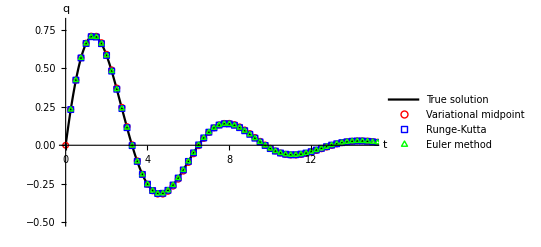

```mathematica
plot=Show[Plot[σ[t],{t,0,tendsmall},PlotStyle->Black,PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[discretepts,Placed["Variational midpoint",Above]],PlotStyle->Red,PlotMarkers->{"○",Scaled[.035]}],
ListPlot[Legended[RKpts,Placed["Runge-Kutta",Above]],PlotStyle->Blue,PlotMarkers->{"□",Scaled[.035]}],
ListPlot[Legended[Eulerpts, Placed["Euler method",Above]],PlotStyle->Green,PlotMarkers->{"△",Scaled[.035]}],
PlotRange->{{0,tendsmall},{-.5,.8}}, 
AxesLabel->{"t","q"}]
```

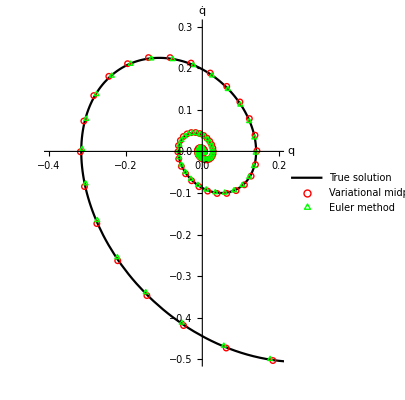

```mathematica
phasespace=Show[
ParametricPlot[{σ[t],σ'[t]},{t,0,tend},PlotStyle->Black,PlotLegends->Placed[{"True solution"},Above]],
ListPlot[Legended[discretevels,Placed["Variational midpoint",Above]],PlotStyle->Red,PlotMarkers->{"○",Scaled[.035]}],
(*ListPlot[Legended[RKvels,Placed["Runge-Kutta",Above]],PlotStyle->Blue,,PlotMarkers->{"□",Scaled[.035]}],*)
ListPlot[Legended[Eulervels, Placed["Euler method",Above]],PlotStyle->Green,PlotMarkers->{"△",Scaled[.035]}],
PlotRange->{{-.4,0.2},{-.5,.3}},
AxesLabel->{"q","q̇"}
]
```

```mathematica
Export["./harmonic_oscillator_phase_space.pdf",phasespace];
```

```mathematica
Export["./harmonic_oscillator_plot.pdf",plot];
```

```mathematica
Momenta[t_]=D[L[q,v],v]/.q->σ[t]/.v->σ'[t];
```

```mathematica
Momentapluspts=Table[{h*n,γp[qrecursive[n-1],qrecursive[n]]},{n,3,Floor[tend/h]}];
```

```mathematica
Momentaminuspts=Table[{h*n,γm[qrecursive[n-1],qrecursive[n],qrecursive[n+1]]},{n,3,Floor[tend/h]}];
```

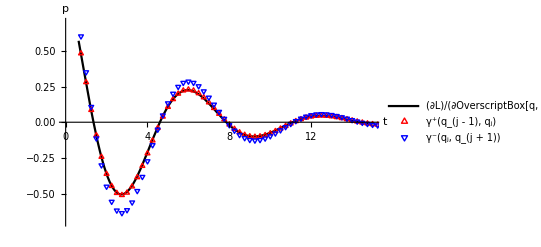

```mathematica
momenta=Show[Plot[Momenta[t],{t,0,tendsmall},PlotStyle->Black,PlotLegends->Placed[{"(∂L)/(∂OverscriptBox[q, .])(q(t),q̇(t))"},Above]],
ListPlot[Legended[Momentapluspts,Placed["γ⁺(q_(j - 1), q_j)",Above]],PlotStyle->Red,PlotMarkers->{"△",Scaled[.035]}],
ListPlot[Legended[Momentaminuspts,Placed["γ⁻(q_j, q_(j + 1))",Above]],PlotStyle->Blue,PlotMarkers->{"▽",Scaled[.035]}],
PlotRange->{{0,tendsmall},{-.7,.7}}, AxesLabel->{"t","p"}]
```

```mathematica
Export["./harmonic_oscillator_momenta.pdf",momenta];
```

```mathematica
(*energypts=Table[{h*n,Hdmimp[qrecursive[n-2],qrecursive[n-1],qrecursive[n]]},{n,2,120}];*)
```

```mathematica
energypts=Table[{h*n,EL[(discretepts[[n]][[2]]+discretepts[[n-1]][[2]])/2,(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])/h]},{n,2,Floor[tend/h]}];
```

```mathematica
energyRKpts=Table[{h*n,EL[RKpts[[n,2]],(2(RKpts[[n+1]][[2]]-RKpts[[n-1]][[2]]))/(3h)+(-RKpts[[n+2]][[2]]+RKpts[[n-2]][[2]])/(12h)]},{n,3,Floor[tend/h]}];
```

Part::partw: Part 402 of {{0.,List},{0.25,0.232566},{0.5,0.424213},{0.75,0.568547},{1.,0.662692},«42»,{11.75,-0.0508048},{12.,-0.0417484},{12.25,-0.0313162},«351»} does not exist.

```mathematica
energyEulerpts=Table[{h*n,EL[(Eulersols[[n]]+Eulersols[[n-1]])/2,(Eulersols[[n]]-Eulersols[[n-1]])/h]},{n,2,Floor[tend/h]}];;
```

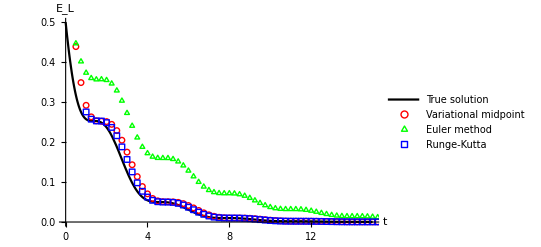

```mathematica
energy=Show[Plot[Energy[t],{t,0,tendsmall},PlotStyle->Black,PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red,PlotMarkers->{"○",Scaled[.035]}],
ListPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green,PlotMarkers->{"△",Scaled[.035]}],
ListPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Blue,PlotMarkers->{"□",Scaled[.035]}],
(*PlotRange->{{0,tend},Automatic},*)
 AxesLabel->{"t","E_L"}]
```

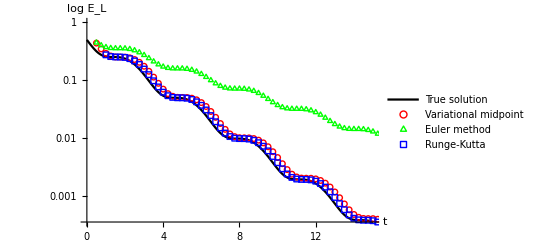

```mathematica
energylog=Show[LogPlot[Energy[t],{t,0,tendsmall},PlotStyle->Black,
PlotLegends->Placed[{"True solution"},Above]],
ListLogPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red,PlotMarkers->{"○",Scaled[.035]}],
ListLogPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green,PlotMarkers->{"△",Scaled[.035]}],
ListLogPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Blue,PlotMarkers->{"□",Scaled[.035]}],
(*PlotRange->{{0,10},Automatic}, *)
(*PlotRange->{{0,100},{-50,0}},*)
AxesLabel->{"t","log E_L"}]
```

```mathematica
Export["./harmonic_oscillator_energy.pdf",energy];
```

```mathematica
Export["./harmonic_oscillator_energy_log.pdf",energylog];
```